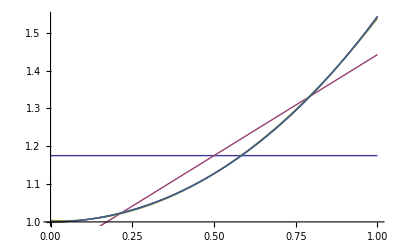

Погрешность приближения равна: 5.26719×10^-6

```mathematica
(*Зададим данную функцию*)
f[x_]=Cosh[x];
(*Зададим отрезок аппроксимации*)
a=0;
b=1;
(*Зададим точность приближения*)
eps=10^(-5);
(*Зададим счетчик количества функций в семействе*)
n=0;
r=Infinity;
(*Зададим переменную для последовательности обобщенных многочленов*)
Phi=List[];
(*Построим семейство обобщенных многочленов, приближающих данную функцию с заданной точностью*)
While[r≥eps,
(*Зададим семейство алгебраических многочленов*)
F=Table[x^k,{k,0,n}];
(*Построим матрицу Грамма*)MGr=Table[Integrate[F[[i]]*F[[j]],{x,a,b}],{i,1,n+1},{j,1,n+1}];
(*Зададим столбец свободных членов системы уравнений*)
B=Table[Integrate[f[x]*F[[i]],{x,a,b}],{i,1,n+1}];
(*Найдем коэффициенты многочлена наилучших среднеквадратических приближений*)
K=Inverse[MGr].B;
(*Добавим очередной многочлен наилучшего среднеквадратического приближения в последовательность*)
AppendTo[Phi,K.F];
n=n+1;
(*Найдем погрешность приближения*)
r=Sqrt[NIntegrate[(f[x]-Phi[[n]])^2,{x,a,b}]];
];
(*Построим графики исходной функции и найденной последовательности обобщенных многочленов в одной системе координат*)
G=Plot[f[x],{x,a,b},PlotStyle->Red];
GPhi=Plot[Phi,{x,a,b}];
Show[G,GPhi]
Print["Погрешность приближения равна: ",r]
```

```mathematica
Animate[Show[G,Plot[Phi[[i]],{x,a,b}]],{i,1,n,1},AnimationRunning->False]
```